```mathematica
<<FormsAndVectors`
SetOptions[Simplify,Trig->False]
```

{Assumptions:>$Assumptions,ComplexityFunction→Automatic,ExcludedForms→{},TimeConstraint→300,TransformationFunctions→Automatic,Trig→False}

-1/80 z^2 (-156-5 z+78 z^2+3 z^3)

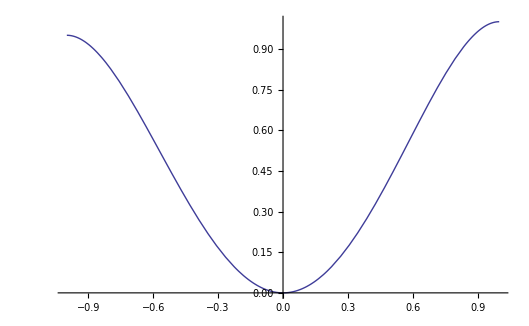

{1/80 (156 Cos[u]^2+5 Cos[u]^3-78 Cos[u]^4-3 Cos[u]^5+80 Cos[v] Sin[u]),13/20 Sin[u] Sin[v],Cos[u]}

{{Sin[u]^2+(Cos[u]^2 (80 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/6400+169/400 Cos[u]^2 Sin[v]^2,-3/400 Cos[u] Sin[u] (77 Cos[v]+5 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v]},{-3/400 Cos[u] Sin[u] (77 Cos[v]+5 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v],169/400 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2}}

1/1600(√(Sin[u]^2 (16375086 Cos[u]^6 Cos[v]^2 Sin[u]^2+1581840 Cos[u]^7 Cos[v]^2 Sin[u]^2+38025 Cos[u]^8 Cos[v]^2 Sin[u]^2+81120 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-40560 Cos[u]^3 Cos[v] Sin[u] (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)+10816 Cos[u]^2 (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)^2+6400 Sin[u]^2 (169 Cos[v]^2+400 Sin[v]^2)+507 Cos[u]^4 Cos[v] Sin[u] (16640 Cos[v]^2-64821 Cos[v] Sin[u]+16640 Sin[v]^2))))

-Graphics3D-

```mathematica
XS={Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]}; 
c=1;
r=19/20;
B=7/20;
DWN[z_,C1_,C2_]:=(z^2/4)*(-3*(C1-C2)*z^3-2*(C1+C2)*z^2+5*(C1-C2)*z+4*(C1+C2));
DWN[z,c,r*c]//Simplify
Plot[DWN[z,c,r*c],{z,-1,1}]
XN=XS+DWN[Cos[u],c,r*c]*{1,0,0}//Simplify;
XNP = XN - B*XS[[2]]*{0,1,0};
X= XNP
g=MetricFromPara[X,u,v]//Simplify
gInv=Inverse[g]//Simplify;
vol= Sqrt[Det[g]]//Simplify
$Assumptions=0<u&&u<π&&0≤v&&v<2π&&t>0&&v>0&&v<2π;
ParametricPlot3D[X,{u,0,π},{v,0,2π}]
```

```mathematica
Xu=D[X,u]//Simplify
Xv=D[X,v]//Simplify
nuDirection=Cross[Xu,Xv]//Simplify;
nu=(1/Sqrt[nuDirection.nuDirection])*nuDirection//Simplify;
```

{1/80 Cos[u] (80 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]),13/20 Cos[u] Sin[v],-Sin[u]}

{-Sin[u] Sin[v],13/20 Cos[v] Sin[u],0}

```mathematica
subsxyz={Cos[u]->z,Sin[u]->Sqrt[1-z^2],Cos[v]->(x-DWN[z,c,r*c])/Sqrt[1-z^2],Sin[v]->y/(1-B)/Sqrt[1-z^2],Cot[u]->z/Sqrt[1-z^2],Csc[u]->1/Sqrt[1-z^2]}//Simplify
```

{Cos[u]→z,Sin[u]→√(1-z^2),Cos[v]→(80 x+z^2 (-156-5 z+78 z^2+3 z^3))/(80 √(1-z^2)),Sin[v]→(20 y)/(13 √(1-z^2)),Cot[u]→z/(√(1-z^2)),Csc[u]→1/(√(1-z^2))}

```mathematica
angle=1/5
vecGlobGen=RotationMatrix[angle,{-1,0,1}].{0,1,0}
1.5*vecGlobGen//N
vec=LocalVecFromPara[vecGlobGen,X,u,v]//Simplify
vecGlob=GlobalVecFromPara[vec,X,u,v]//Simplify
vecR3=TrigExpand[vecGlob]//.subsxyz//Simplify
vecR3Para=(vecR3[[1]]*iHat+vecR3[[2]]*jHat+vecR3[[3]]*kHat)/.{x->coordsX,y->coordsY,z->coordsZ}//InputForm
```

1/5

{-Sin[1/5]/(√2),Cos[1/5],-Sin[1/5]/(√2)}

{-0.210721,1.4701,-0.210721}

{-(40 (-195 Cos[u]^2 Cos[v] Sin[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v])+4056 Cos[u]^3 Cos[v] Sin[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v])+195 Cos[u]^4 Cos[v] Sin[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v])+104 Cos[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v]) (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)-80 √2 Sin[1/5] Sin[u] (169 Cos[v]^2+400 Sin[v]^2)))/(16375086 Cos[u]^6 Cos[v]^2 Sin[u]^2+1581840 Cos[u]^7 Cos[v]^2 Sin[u]^2+38025 Cos[u]^8 Cos[v]^2 Sin[u]^2+81120 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-40560 Cos[u]^3 Cos[v] Sin[u] (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)+10816 Cos[u]^2 (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)^2+6400 Sin[u]^2 (169 Cos[v]^2+400 Sin[v]^2)+507 Cos[u]^4 Cos[v] Sin[u] (16640 Cos[v]^2-64821 Cos[v] Sin[u]+16640 Sin[v]^2)),(3/400 Cos[u] Sin[u] (77 Cos[v]+5 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v] ((Sin[1/5] Sin[u])/(√2)-(Cos[u] Sin[1/5] (80 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]))/(80 √2)+13/20 Cos[1/5] Cos[u] Sin[v])+(13/20 Cos[1/5] Cos[v] Sin[u]+(Sin[1/5] Sin[u] Sin[v])/(√2)) (Sin[u]^2+(Cos[u]^2 (80 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/6400+169/400 Cos[u]^2 Sin[v]^2))/(-(9 Cos[u]^2 Sin[u]^2 (77 Cos[v]+5 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/160000+(Sin[u]^2+(Cos[u]^2 (80 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/6400+169/400 Cos[u]^2 Sin[v]^2) (169/400 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2))}

{-(16375086 √2 Cos[u]^6 Cos[v]^2 Sin[1/5] Sin[u]^2+1581840 √2 Cos[u]^7 Cos[v]^2 Sin[1/5] Sin[u]^2+38025 √2 Cos[u]^8 Cos[v]^2 Sin[1/5] Sin[u]^2+256000 Sin[u]^2 Sin[v] (13 Cos[1/5] Cos[v]+10 √2 Sin[1/5] Sin[v])-202800 √2 Cos[u]^3 Cos[v] Sin[1/5] Sin[u] (2 Cos[v]^2+13 Cos[v] Sin[u]+2 Sin[v]^2)+81120 √2 Cos[u]^5 Cos[v] Sin[1/5] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-108160 √2 Cos[u] Cos[v] Sin[1/5] Sin[u] (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)+6591 √2 Cos[u]^4 Cos[v] Sin[1/5] Sin[u] (1280 Cos[v]^2-5017 Cos[v] Sin[u]+1280 Sin[v]^2)+2704 √2 Cos[u]^2 Sin[1/5] (400 Cos[v]^4-3120 Cos[v]^3 Sin[u]-3120 Cos[v] Sin[u] Sin[v]^2+400 Sin[v]^4+Cos[v]^2 (6159 Sin[u]^2+800 Sin[v]^2)))/(2 (16375086 Cos[u]^6 Cos[v]^2 Sin[u]^2+1581840 Cos[u]^7 Cos[v]^2 Sin[u]^2+38025 Cos[u]^8 Cos[v]^2 Sin[u]^2+81120 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-40560 Cos[u]^3 Cos[v] Sin[u] (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)+10816 Cos[u]^2 (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)^2+6400 Sin[u]^2 (169 Cos[v]^2+400 Sin[v]^2)+507 Cos[u]^4 Cos[v] Sin[u] (16640 Cos[v]^2-64821 Cos[v] Sin[u]+16640 Sin[v]^2))),(13 (1259622 Cos[1/5] Cos[u]^6 Cos[v]^2 Sin[u]^2+121680 Cos[1/5] Cos[u]^7 Cos[v]^2 Sin[u]^2+2925 Cos[1/5] Cos[u]^8 Cos[v]^2 Sin[u]^2+6400 Cos[v] Sin[u]^2 (13 Cos[1/5] Cos[v]+10 √2 Sin[1/5] Sin[v])+6240 Cos[1/5] Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+6400 √2 Cos[u] Sin[1/5] Sin[u] Sin[v] (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)-3120 Cos[u]^3 Cos[v] Sin[u] (10 Cos[1/5] Cos[v]^2-39 Cos[1/5] Cos[v] Sin[u]+10 Sin[v] (-8 √2 Sin[1/5] Sin[u]+Cos[1/5] Sin[v]))+3 Cos[u]^4 Cos[v] Sin[u] (216320 Cos[1/5] Cos[v]^2-842673 Cos[1/5] Cos[v] Sin[u]+160 Sin[v] (25 √2 Sin[1/5] Sin[u]+1352 Cos[1/5] Sin[v]))+32 Cos[u]^2 (2600 Cos[1/5] Cos[v]^4-20280 Cos[1/5] Cos[v]^3 Sin[u]+2600 Cos[1/5] Sin[v]^4-15 Cos[v] Sin[u] Sin[v] (25 √2 Sin[1/5] Sin[u]+1352 Cos[1/5] Sin[v])+26 Cos[1/5] Cos[v]^2 (1521 Sin[u]^2+200 Sin[v]^2))))/(16375086 Cos[u]^6 Cos[v]^2 Sin[u]^2+1581840 Cos[u]^7 Cos[v]^2 Sin[u]^2+38025 Cos[u]^8 Cos[v]^2 Sin[u]^2+81120 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-40560 Cos[u]^3 Cos[v] Sin[u] (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)+10816 Cos[u]^2 (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)^2+6400 Sin[u]^2 (169 Cos[v]^2+400 Sin[v]^2)+507 Cos[u]^4 Cos[v] Sin[u] (16640 Cos[v]^2-64821 Cos[v] Sin[u]+16640 Sin[v]^2)),(40 Sin[u] (-195 Cos[u]^2 Cos[v] Sin[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v])+4056 Cos[u]^3 Cos[v] Sin[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v])+195 Cos[u]^4 Cos[v] Sin[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v])+104 Cos[u] (13 √2 Cos[v] Sin[1/5]-40 Cos[1/5] Sin[v]) (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)-80 √2 Sin[1/5] Sin[u] (169 Cos[v]^2+400 Sin[v]^2)))/(16375086 Cos[u]^6 Cos[v]^2 Sin[u]^2+1581840 Cos[u]^7 Cos[v]^2 Sin[u]^2+38025 Cos[u]^8 Cos[v]^2 Sin[u]^2+81120 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-40560 Cos[u]^3 Cos[v] Sin[u] (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)+10816 Cos[u]^2 (10 Cos[v]^2-39 Cos[v] Sin[u]+10 Sin[v]^2)^2+6400 Sin[u]^2 (169 Cos[v]^2+400 Sin[v]^2)+507 Cos[u]^4 Cos[v] Sin[u] (16640 Cos[v]^2-64821 Cos[v] Sin[u]+16640 Sin[v]^2))}

{-((-1+z^2)^2 (138444800000 y z^2 (-156-5 z+78 z^2+3 z^3) Cos[1/5]+1081600 √2 x^2 (-2560000+4218240 z+16653936 z^2-2636400 z^3-33067047 z^4-3163680 z^5+16375086 z^6+1581840 z^7+38025 z^8) Sin[1/5]-2560000 √2 y^2 (-2560000+4218240 z+16653936 z^2-2636400 z^3-33067047 z^4-3163680 z^5+16375086 z^6+1581840 z^7+38025 z^8) Sin[1/5]+169 √2 (16384000000+26996736000 z+104045670400 z^2-16872960000 z^3-169074630400 z^4+98661488640 z^5+474479952896 z^6-131948993280 z^7-1236232105728 z^8-69733776216 z^9+1304711146977 z^10+189567310140 z^11-590544646380 z^12-101148465132 z^13+93717701766 z^14+17146275588 z^15+1117880244 z^16+32032260 z^17+342225 z^18) Sin[1/5]+27040 x (409600000 y Cos[1/5]+√2 z (-86528000-275558400 z-677693440 z^2-2143866816 z^3+681799440 z^4+6483303060 z^5+503191923 z^6-5125833882 z^7-674610651 z^8+1253924568 z^9+172318653 z^10+7711470 z^11+114075 z^12) Sin[1/5])))/(4 (1169858560000 x^4 z^2+6553600000000 y^4 z^2-29246464000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+28561 z^4 (156+5 z-78 z^2-3 z^3)^2 (6400+84544 z^2+9360 z^3-285407 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)+1081600 x^2 (1081600+64 (223249+80000 y^2) z^2+1581840 z^3-15331511 z^4-2372760 z^5-76050 z^6+1028196 z^7+8281338 z^8+158184 z^9-2071602 z^10-79092 z^11+1521 z^12)-5120000 y^2 (-1280000+2560000 z^2-9505568 z^4-659100 z^5+16438461 z^6+1410474 z^7-12309622 z^8-1080924 z^9+3061773 z^10+276822 z^11+6084 z^12)+27040 x z^2 (-2560000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+169 (-998400-32000 z-12689664 z^2-1863680 z^3+43478292 z^4+6182827 z^5-59963826 z^6-8664702 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))),(169 (-1+z^2)^2 (1081600 x^2 (6400+97344 z^2+9360 z^3-194463 z^4-18720 z^5+96894 z^6+9360 z^7+225 z^8) Cos[1/5]-2560000 y^2 (6400+97344 z^2+9360 z^3-194463 z^4-18720 z^5+96894 z^6+9360 z^7+225 z^8) Cos[1/5]+169 (40960000+663961600 z^2+59904000 z^3-465811200 z^4-69888000 z^5+2210973184 z^6+394617600 z^7-7044386352 z^8-1156520664 z^9+7629427593 z^10+1269962460 z^11-3475411740 z^12-597725388 z^13+554553414 z^14+101457252 z^15+6614676 z^16+189540 z^17+2025 z^18) Cos[1/5]+2560000 √2 y z (6400-12480 z+48272 z^2+10140 z^3-72693 z^4-6006 z^5+24216 z^6+2106 z^7+45 z^8) Sin[1/5]+160 x (-293329920 z^5 Cos[1/5]+6402101940 z^6 Cos[1/5]+830592243 z^7 Cos[1/5]-5097360762 z^8 Cos[1/5]-674002251 z^9 Cos[1/5]+1253924568 z^10 Cos[1/5]+172318653 z^11 Cos[1/5]+7711470 z^12 Cos[1/5]+114075 z^13 Cos[1/5]+102400000 √2 y Sin[1/5]-399360000 √2 y z Sin[1/5]-768 z^4 (2352987 Cos[1/5]-25000 √2 y Sin[1/5])-416000 z^3 (91 Cos[1/5]-960 √2 y Sin[1/5])-384000 z^2 (2197 Cos[1/5]+50 √2 y Sin[1/5]))))/(2 (1169858560000 x^4 z^2+6553600000000 y^4 z^2-29246464000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+28561 z^4 (156+5 z-78 z^2-3 z^3)^2 (6400+84544 z^2+9360 z^3-285407 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)+1081600 x^2 (1081600+64 (223249+80000 y^2) z^2+1581840 z^3-15331511 z^4-2372760 z^5-76050 z^6+1028196 z^7+8281338 z^8+158184 z^9-2071602 z^10-79092 z^11+1521 z^12)-5120000 y^2 (-1280000+2560000 z^2-9505568 z^4-659100 z^5+16438461 z^6+1410474 z^7-12309622 z^8-1080924 z^9+3061773 z^10+276822 z^11+6084 z^12)+27040 x z^2 (-2560000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+169 (-998400-32000 z-12689664 z^2-1863680 z^3+43478292 z^4+6182827 z^5-59963826 z^6-8664702 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))),(20 (-1+z^2)^2 (-21632000 y z (6400+48672 z^2+3900 z^3-72933 z^4-6006 z^5+24216 z^6+2106 z^7+45 z^8+240 x (-104-5 z+104 z^2+5 z^3)) Cos[1/5]-7680000 √2 y^2 (6160-17576 z-845 z^2+17576 z^3+845 z^4) Sin[1/5]+169 √2 (-291328000-337459200 z+275104000 z^2+337459200 z^3+471361280 z^4-1423089408 z^5-602949120 z^6+2529392736 z^7+407934993 z^8-1584132420 z^9-191966907 z^10+313204320 z^11+40000779 z^12+1660932 z^13+22815 z^14+19200 x^2 (6160-17576 z-845 z^2+17576 z^3+845 z^4)+160 x z (1081600-2882880 z+8133168 z^2+2100540 z^3-12270237 z^4-1015014 z^5+4092504 z^6+355914 z^7+7605 z^8)) Sin[1/5]))/(1169858560000 x^4 z^2+6553600000000 y^4 z^2-29246464000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+28561 z^4 (156+5 z-78 z^2-3 z^3)^2 (6400+84544 z^2+9360 z^3-285407 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)+1081600 x^2 (1081600+64 (223249+80000 y^2) z^2+1581840 z^3-15331511 z^4-2372760 z^5-76050 z^6+1028196 z^7+8281338 z^8+158184 z^9-2071602 z^10-79092 z^11+1521 z^12)-5120000 y^2 (-1280000+2560000 z^2-9505568 z^4-659100 z^5+16438461 z^6+1410474 z^7-12309622 z^8-1080924 z^9+3061773 z^10+276822 z^11+6084 z^12)+27040 x z^2 (-2560000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+169 (-998400-32000 z-12689664 z^2-1863680 z^3+43478292 z^4+6182827 z^5-59963826 z^6-8664702 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))}

(20*(-1 + coordsZ^2)^2*kHat*(-21632000*coordsY*coordsZ*(6400 + 48672*coordsZ^2 + 3900*coordsZ^3 - 72933*coordsZ^4 - 6006*coordsZ^5 + 
      24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8 + 240*coordsX*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3))*Cos[1/5] - 
    7680000*Sqrt[2]*coordsY^2*(6160 - 17576*coordsZ - 845*coordsZ^2 + 17576*coordsZ^3 + 845*coordsZ^4)*Sin[1/5] + 
    169*Sqrt[2]*(-291328000 - 337459200*coordsZ + 275104000*coordsZ^2 + 337459200*coordsZ^3 + 471361280*coordsZ^4 - 1423089408*coordsZ^5 - 
      602949120*coordsZ^6 + 2529392736*coordsZ^7 + 407934993*coordsZ^8 - 1584132420*coordsZ^9 - 191966907*coordsZ^10 + 313204320*coordsZ^11 + 
      40000779*coordsZ^12 + 1660932*coordsZ^13 + 22815*coordsZ^14 + 19200*coordsX^2*(6160 - 17576*coordsZ - 845*coordsZ^2 + 17576*coordsZ^3 + 
        845*coordsZ^4) + 160*coordsX*coordsZ*(1081600 - 2882880*coordsZ + 8133168*coordsZ^2 + 2100540*coordsZ^3 - 12270237*coordsZ^4 - 
        1015014*coordsZ^5 + 4092504*coordsZ^6 + 355914*coordsZ^7 + 7605*coordsZ^8))*Sin[1/5]))/
  (1169858560000*coordsX^4*coordsZ^2 + 6553600000000*coordsY^4*coordsZ^2 - 29246464000*coordsX^3*coordsZ^2*
    (312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
   28561*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(6400 + 84544*coordsZ^2 + 9360*coordsZ^3 - 285407*coordsZ^4 - 
     29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
     144*coordsZ^12) + 1081600*coordsX^2*(1081600 + 64*(223249 + 80000*coordsY^2)*coordsZ^2 + 1581840*coordsZ^3 - 15331511*coordsZ^4 - 
     2372760*coordsZ^5 - 76050*coordsZ^6 + 1028196*coordsZ^7 + 8281338*coordsZ^8 + 158184*coordsZ^9 - 2071602*coordsZ^10 - 79092*coordsZ^11 + 
     1521*coordsZ^12) - 5120000*coordsY^2*(-1280000 + 2560000*coordsZ^2 - 9505568*coordsZ^4 - 659100*coordsZ^5 + 16438461*coordsZ^6 + 
     1410474*coordsZ^7 - 12309622*coordsZ^8 - 1080924*coordsZ^9 + 3061773*coordsZ^10 + 276822*coordsZ^11 + 6084*coordsZ^12) + 
   27040*coordsX*coordsZ^2*(-2560000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
     169*(-998400 - 32000*coordsZ - 12689664*coordsZ^2 - 1863680*coordsZ^3 + 43478292*coordsZ^4 + 6182827*coordsZ^5 - 59963826*coordsZ^6 - 
       8664702*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
       417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))) - 
 ((-1 + coordsZ^2)^2*iHat*(138444800000*coordsY*coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3)*Cos[1/5] + 
    1081600*Sqrt[2]*coordsX^2*(-2560000 + 4218240*coordsZ + 16653936*coordsZ^2 - 2636400*coordsZ^3 - 33067047*coordsZ^4 - 3163680*coordsZ^5 + 
      16375086*coordsZ^6 + 1581840*coordsZ^7 + 38025*coordsZ^8)*Sin[1/5] - 2560000*Sqrt[2]*coordsY^2*
     (-2560000 + 4218240*coordsZ + 16653936*coordsZ^2 - 2636400*coordsZ^3 - 33067047*coordsZ^4 - 3163680*coordsZ^5 + 16375086*coordsZ^6 + 
      1581840*coordsZ^7 + 38025*coordsZ^8)*Sin[1/5] + 169*Sqrt[2]*(16384000000 + 26996736000*coordsZ + 104045670400*coordsZ^2 - 
      16872960000*coordsZ^3 - 169074630400*coordsZ^4 + 98661488640*coordsZ^5 + 474479952896*coordsZ^6 - 131948993280*coordsZ^7 - 
      1236232105728*coordsZ^8 - 69733776216*coordsZ^9 + 1304711146977*coordsZ^10 + 189567310140*coordsZ^11 - 590544646380*coordsZ^12 - 
      101148465132*coordsZ^13 + 93717701766*coordsZ^14 + 17146275588*coordsZ^15 + 1117880244*coordsZ^16 + 32032260*coordsZ^17 + 
      342225*coordsZ^18)*Sin[1/5] + 27040*coordsX*(409600000*coordsY*Cos[1/5] + 
      Sqrt[2]*coordsZ*(-86528000 - 275558400*coordsZ - 677693440*coordsZ^2 - 2143866816*coordsZ^3 + 681799440*coordsZ^4 + 
        6483303060*coordsZ^5 + 503191923*coordsZ^6 - 5125833882*coordsZ^7 - 674610651*coordsZ^8 + 1253924568*coordsZ^9 + 172318653*coordsZ^10 + 
        7711470*coordsZ^11 + 114075*coordsZ^12)*Sin[1/5])))/(4*(1169858560000*coordsX^4*coordsZ^2 + 6553600000000*coordsY^4*coordsZ^2 - 
    29246464000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
    28561*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(6400 + 84544*coordsZ^2 + 9360*coordsZ^3 - 285407*coordsZ^4 - 
      29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
      144*coordsZ^12) + 1081600*coordsX^2*(1081600 + 64*(223249 + 80000*coordsY^2)*coordsZ^2 + 1581840*coordsZ^3 - 15331511*coordsZ^4 - 
      2372760*coordsZ^5 - 76050*coordsZ^6 + 1028196*coordsZ^7 + 8281338*coordsZ^8 + 158184*coordsZ^9 - 2071602*coordsZ^10 - 79092*coordsZ^11 + 
      1521*coordsZ^12) - 5120000*coordsY^2*(-1280000 + 2560000*coordsZ^2 - 9505568*coordsZ^4 - 659100*coordsZ^5 + 16438461*coordsZ^6 + 
      1410474*coordsZ^7 - 12309622*coordsZ^8 - 1080924*coordsZ^9 + 3061773*coordsZ^10 + 276822*coordsZ^11 + 6084*coordsZ^12) + 
    27040*coordsX*coordsZ^2*(-2560000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
      169*(-998400 - 32000*coordsZ - 12689664*coordsZ^2 - 1863680*coordsZ^3 + 43478292*coordsZ^4 + 6182827*coordsZ^5 - 59963826*coordsZ^6 - 
        8664702*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
        417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))) + 
 (169*(-1 + coordsZ^2)^2*jHat*(1081600*coordsX^2*(6400 + 97344*coordsZ^2 + 9360*coordsZ^3 - 194463*coordsZ^4 - 18720*coordsZ^5 + 
      96894*coordsZ^6 + 9360*coordsZ^7 + 225*coordsZ^8)*Cos[1/5] - 2560000*coordsY^2*(6400 + 97344*coordsZ^2 + 9360*coordsZ^3 - 
      194463*coordsZ^4 - 18720*coordsZ^5 + 96894*coordsZ^6 + 9360*coordsZ^7 + 225*coordsZ^8)*Cos[1/5] + 
    169*(40960000 + 663961600*coordsZ^2 + 59904000*coordsZ^3 - 465811200*coordsZ^4 - 69888000*coordsZ^5 + 2210973184*coordsZ^6 + 
      394617600*coordsZ^7 - 7044386352*coordsZ^8 - 1156520664*coordsZ^9 + 7629427593*coordsZ^10 + 1269962460*coordsZ^11 - 
      3475411740*coordsZ^12 - 597725388*coordsZ^13 + 554553414*coordsZ^14 + 101457252*coordsZ^15 + 6614676*coordsZ^16 + 189540*coordsZ^17 + 
      2025*coordsZ^18)*Cos[1/5] + 2560000*Sqrt[2]*coordsY*coordsZ*(6400 - 12480*coordsZ + 48272*coordsZ^2 + 10140*coordsZ^3 - 72693*coordsZ^4 - 
      6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8)*Sin[1/5] + 
    160*coordsX*(-293329920*coordsZ^5*Cos[1/5] + 6402101940*coordsZ^6*Cos[1/5] + 830592243*coordsZ^7*Cos[1/5] - 5097360762*coordsZ^8*Cos[1/5] - 
      674002251*coordsZ^9*Cos[1/5] + 1253924568*coordsZ^10*Cos[1/5] + 172318653*coordsZ^11*Cos[1/5] + 7711470*coordsZ^12*Cos[1/5] + 
      114075*coordsZ^13*Cos[1/5] + 102400000*Sqrt[2]*coordsY*Sin[1/5] - 399360000*Sqrt[2]*coordsY*coordsZ*Sin[1/5] - 
      768*coordsZ^4*(2352987*Cos[1/5] - 25000*Sqrt[2]*coordsY*Sin[1/5]) - 416000*coordsZ^3*(91*Cos[1/5] - 960*Sqrt[2]*coordsY*Sin[1/5]) - 
      384000*coordsZ^2*(2197*Cos[1/5] + 50*Sqrt[2]*coordsY*Sin[1/5]))))/
  (2*(1169858560000*coordsX^4*coordsZ^2 + 6553600000000*coordsY^4*coordsZ^2 - 29246464000*coordsX^3*coordsZ^2*
     (312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
    28561*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(6400 + 84544*coordsZ^2 + 9360*coordsZ^3 - 285407*coordsZ^4 - 
      29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
      144*coordsZ^12) + 1081600*coordsX^2*(1081600 + 64*(223249 + 80000*coordsY^2)*coordsZ^2 + 1581840*coordsZ^3 - 15331511*coordsZ^4 - 
      2372760*coordsZ^5 - 76050*coordsZ^6 + 1028196*coordsZ^7 + 8281338*coordsZ^8 + 158184*coordsZ^9 - 2071602*coordsZ^10 - 79092*coordsZ^11 + 
      1521*coordsZ^12) - 5120000*coordsY^2*(-1280000 + 2560000*coordsZ^2 - 9505568*coordsZ^4 - 659100*coordsZ^5 + 16438461*coordsZ^6 + 
      1410474*coordsZ^7 - 12309622*coordsZ^8 - 1080924*coordsZ^9 + 3061773*coordsZ^10 + 276822*coordsZ^11 + 6084*coordsZ^12) + 
    27040*coordsX*coordsZ^2*(-2560000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
      169*(-998400 - 32000*coordsZ - 12689664*coordsZ^2 - 1863680*coordsZ^3 + 43478292*coordsZ^4 + 6182827*coordsZ^5 - 59963826*coordsZ^6 - 
        8664702*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
        417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))))

```mathematica
StringReplace[ToString[vecR3Para],{"Sqrt"->"sqrt","Cos"->"cos","Sin"->"sin","["->"(","]"->")","Pi"->ToString[π//N]}]//FullForm
```

"(20*(-1 + coordsZ^2)^2*kHat*(-21632000*coordsY*coordsZ*(6400 + 48672*coordsZ^2 + 3900*coordsZ^3 - 72933*coordsZ^4 - 6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8 + 240*coordsX*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3))*cos(1/5) - 7680000*sqrt(2)*coordsY^2*(6160 - 17576*coordsZ - 845*coordsZ^2 + 17576*coordsZ^3 + 845*coordsZ^4)*sin(1/5) + 169*sqrt(2)*(-291328000 - 337459200*coordsZ + 275104000*coordsZ^2 + 337459200*coordsZ^3 + 471361280*coordsZ^4 - 1423089408*coordsZ^5 - 602949120*coordsZ^6 + 2529392736*coordsZ^7 + 407934993*coordsZ^8 - 1584132420*coordsZ^9 - 191966907*coordsZ^10 + 313204320*coordsZ^11 + 40000779*coordsZ^12 + 1660932*coordsZ^13 + 22815*coordsZ^14 + 19200*coordsX^2*(6160 - 17576*coordsZ - 845*coordsZ^2 + 17576*coordsZ^3 + 845*coordsZ^4) + 160*coordsX*coordsZ*(1081600 - 2882880*coordsZ + 8133168*coordsZ^2 + 2100540*coordsZ^3 - 12270237*coordsZ^4 - 1015014*coordsZ^5 + 4092504*coordsZ^6 + 355914*coordsZ^7 + 7605*coordsZ^8))*sin(1/5)))/(1169858560000*coordsX^4*coordsZ^2 + 6553600000000*coordsY^4*coordsZ^2 - 29246464000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 28561*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(6400 + 84544*coordsZ^2 + 9360*coordsZ^3 - 285407*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) + 1081600*coordsX^2*(1081600 + 64*(223249 + 80000*coordsY^2)*coordsZ^2 + 1581840*coordsZ^3 - 15331511*coordsZ^4 - 2372760*coordsZ^5 - 76050*coordsZ^6 + 1028196*coordsZ^7 + 8281338*coordsZ^8 + 158184*coordsZ^9 - 2071602*coordsZ^10 - 79092*coordsZ^11 + 1521*coordsZ^12) - 5120000*coordsY^2*(-1280000 + 2560000*coordsZ^2 - 9505568*coordsZ^4 - 659100*coordsZ^5 + 16438461*coordsZ^6 + 1410474*coordsZ^7 - 12309622*coordsZ^8 - 1080924*coordsZ^9 + 3061773*coordsZ^10 + 276822*coordsZ^11 + 6084*coordsZ^12) + 27040*coordsX*coordsZ^2*(-2560000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 169*(-998400 - 32000*coordsZ - 12689664*coordsZ^2 - 1863680*coordsZ^3 + 43478292*coordsZ^4 + 6182827*coordsZ^5 - 59963826*coordsZ^6 - 8664702*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))) - ((-1 + coordsZ^2)^2*iHat*(138444800000*coordsY*coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3)*cos(1/5) + 1081600*sqrt(2)*coordsX^2*(-2560000 + 4218240*coordsZ + 16653936*coordsZ^2 - 2636400*coordsZ^3 - 33067047*coordsZ^4 - 3163680*coordsZ^5 + 16375086*coordsZ^6 + 1581840*coordsZ^7 + 38025*coordsZ^8)*sin(1/5) - 2560000*sqrt(2)*coordsY^2*(-2560000 + 4218240*coordsZ + 16653936*coordsZ^2 - 2636400*coordsZ^3 - 33067047*coordsZ^4 - 3163680*coordsZ^5 + 16375086*coordsZ^6 + 1581840*coordsZ^7 + 38025*coordsZ^8)*sin(1/5) + 169*sqrt(2)*(16384000000 + 26996736000*coordsZ + 104045670400*coordsZ^2 - 16872960000*coordsZ^3 - 169074630400*coordsZ^4 + 98661488640*coordsZ^5 + 474479952896*coordsZ^6 - 131948993280*coordsZ^7 - 1236232105728*coordsZ^8 - 69733776216*coordsZ^9 + 1304711146977*coordsZ^10 + 189567310140*coordsZ^11 - 590544646380*coordsZ^12 - 101148465132*coordsZ^13 + 93717701766*coordsZ^14 + 17146275588*coordsZ^15 + 1117880244*coordsZ^16 + 32032260*coordsZ^17 + 342225*coordsZ^18)*sin(1/5) + 27040*coordsX*(409600000*coordsY*cos(1/5) + sqrt(2)*coordsZ*(-86528000 - 275558400*coordsZ - 677693440*coordsZ^2 - 2143866816*coordsZ^3 + 681799440*coordsZ^4 + 6483303060*coordsZ^5 + 503191923*coordsZ^6 - 5125833882*coordsZ^7 - 674610651*coordsZ^8 + 1253924568*coordsZ^9 + 172318653*coordsZ^10 + 7711470*coordsZ^11 + 114075*coordsZ^12)*sin(1/5))))/(4*(1169858560000*coordsX^4*coordsZ^2 + 6553600000000*coordsY^4*coordsZ^2 - 29246464000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 28561*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(6400 + 84544*coordsZ^2 + 9360*coordsZ^3 - 285407*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) + 1081600*coordsX^2*(1081600 + 64*(223249 + 80000*coordsY^2)*coordsZ^2 + 1581840*coordsZ^3 - 15331511*coordsZ^4 - 2372760*coordsZ^5 - 76050*coordsZ^6 + 1028196*coordsZ^7 + 8281338*coordsZ^8 + 158184*coordsZ^9 - 2071602*coordsZ^10 - 79092*coordsZ^11 + 1521*coordsZ^12) - 5120000*coordsY^2*(-1280000 + 2560000*coordsZ^2 - 9505568*coordsZ^4 - 659100*coordsZ^5 + 16438461*coordsZ^6 + 1410474*coordsZ^7 - 12309622*coordsZ^8 - 1080924*coordsZ^9 + 3061773*coordsZ^10 + 276822*coordsZ^11 + 6084*coordsZ^12) + 27040*coordsX*coordsZ^2*(-2560000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 169*(-998400 - 32000*coordsZ - 12689664*coordsZ^2 - 1863680*coordsZ^3 + 43478292*coordsZ^4 + 6182827*coordsZ^5 - 59963826*coordsZ^6 - 8664702*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))) + (169*(-1 + coordsZ^2)^2*jHat*(1081600*coordsX^2*(6400 + 97344*coordsZ^2 + 9360*coordsZ^3 - 194463*coordsZ^4 - 18720*coordsZ^5 + 96894*coordsZ^6 + 9360*coordsZ^7 + 225*coordsZ^8)*cos(1/5) - 2560000*coordsY^2*(6400 + 97344*coordsZ^2 + 9360*coordsZ^3 - 194463*coordsZ^4 - 18720*coordsZ^5 + 96894*coordsZ^6 + 9360*coordsZ^7 + 225*coordsZ^8)*cos(1/5) + 169*(40960000 + 663961600*coordsZ^2 + 59904000*coordsZ^3 - 465811200*coordsZ^4 - 69888000*coordsZ^5 + 2210973184*coordsZ^6 + 394617600*coordsZ^7 - 7044386352*coordsZ^8 - 1156520664*coordsZ^9 + 7629427593*coordsZ^10 + 1269962460*coordsZ^11 - 3475411740*coordsZ^12 - 597725388*coordsZ^13 + 554553414*coordsZ^14 + 101457252*coordsZ^15 + 6614676*coordsZ^16 + 189540*coordsZ^17 + 2025*coordsZ^18)*cos(1/5) + 2560000*sqrt(2)*coordsY*coordsZ*(6400 - 12480*coordsZ + 48272*coordsZ^2 + 10140*coordsZ^3 - 72693*coordsZ^4 - 6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8)*sin(1/5) + 160*coordsX*(-293329920*coordsZ^5*cos(1/5) + 6402101940*coordsZ^6*cos(1/5) + 830592243*coordsZ^7*cos(1/5) - 5097360762*coordsZ^8*cos(1/5) - 674002251*coordsZ^9*cos(1/5) + 1253924568*coordsZ^10*cos(1/5) + 172318653*coordsZ^11*cos(1/5) + 7711470*coordsZ^12*cos(1/5) + 114075*coordsZ^13*cos(1/5) + 102400000*sqrt(2)*coordsY*sin(1/5) - 399360000*sqrt(2)*coordsY*coordsZ*sin(1/5) - 768*coordsZ^4*(2352987*cos(1/5) - 25000*sqrt(2)*coordsY*sin(1/5)) - 416000*coordsZ^3*(91*cos(1/5) - 960*sqrt(2)*coordsY*sin(1/5)) - 384000*coordsZ^2*(2197*cos(1/5) + 50*sqrt(2)*coordsY*sin(1/5)))))/(2*(1169858560000*coordsX^4*coordsZ^2 + 6553600000000*coordsY^4*coordsZ^2 - 29246464000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 28561*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(6400 + 84544*coordsZ^2 + 9360*coordsZ^3 - 285407*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) + 1081600*coordsX^2*(1081600 + 64*(223249 + 80000*coordsY^2)*coordsZ^2 + 1581840*coordsZ^3 - 15331511*coordsZ^4 - 2372760*coordsZ^5 - 76050*coordsZ^6 + 1028196*coordsZ^7 + 8281338*coordsZ^8 + 158184*coordsZ^9 - 2071602*coordsZ^10 - 79092*coordsZ^11 + 1521*coordsZ^12) - 5120000*coordsY^2*(-1280000 + 2560000*coordsZ^2 - 9505568*coordsZ^4 - 659100*coordsZ^5 + 16438461*coordsZ^6 + 1410474*coordsZ^7 - 12309622*coordsZ^8 - 1080924*coordsZ^9 + 3061773*coordsZ^10 + 276822*coordsZ^11 + 6084*coordsZ^12) + 27040*coordsX*coordsZ^2*(-2560000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 169*(-998400 - 32000*coordsZ - 12689664*coordsZ^2 - 1863680*coordsZ^3 + 43478292*coordsZ^4 + 6182827*coordsZ^5 - 59963826*coordsZ^6 - 8664702*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))))"

```mathematica
RotationMatrix[phi,{-1,0,1}]//MatrixForm
```

(1/2 (1+Cos[phi]) | -Sin[phi]/(√2) | 1/2 (-1+Cos[phi])
Sin[phi]/(√2) | Cos[phi] | Sin[phi]/(√2)
1/2 (-1+Cos[phi]) | -Sin[phi]/(√2) | 1/2 (1+Cos[phi]))